```mathematica
Clear["`*"]
```

## Diffusion for curved source

### Set style of plots

```mathematica
$PlotTheme="ModStyle";
Themes`AddThemeRules["ModStyle",DefaultPlotStyle->Thread@Directive[ColorData[112,"ColorList"],Thick],Frame->True,LabelStyle->{Black,20,FontFamily->"Arial"},AxesStyle->Black,TicksStyle->Black,FrameStyle->Black,FrameTicksStyle->Black,Background->None,PlotRangePadding->0,RotateLabel->False];
```

### (c) Analytical Expression for different values of √(D τ)κ

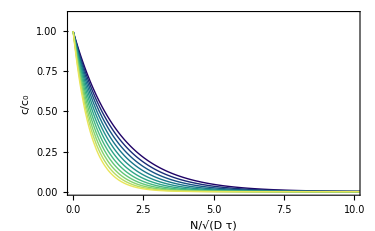

```mathematica
p1=Plot[Evaluate@Table[ⅇ^(-1/2 x (κ+√(4+κ^2))),{κ,-1,1,0.2}],{x,0,20},PlotRange->{{0,10},{0,1.1}},PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{-1,1}},LabelStyle->{FontFamily->"Arial",Black,FontSize->18},LegendMarkerSize->200,LegendFunction->"Frame",LegendLayout->"Row",LegendLabel->"√(D τ)κ"],{0.6,0.6}],PlotStyle->Table[ColorData["BlueGreenYellow"][κ+0.5],{κ,-0.5,0.5,0.1}],FrameLabel->{"N/√(D τ)","c/c_0"},ImageSize->375]
```

### (d) Simulation in semi-circle

```mathematica
(*Define function that solves the diffusion equation in the geometry of semi-circle + rectangle*)
SolveDiffusionCirc[CaseChoice_,Rad_,Dτval_,u0_]:=Module[{bd,solu,mesh,BVs,BCs,reg1,reg2},Needs["NDSolve`FEM`"];
(*Define the boundary.*)
bd=Max[20,1.5*Rad];SquareBox={bd-x,bd+x,bd-y,y,y+bd};
(*Define the two regions (positive or negative curvature)*)
reg1={bd-x>0&&bd+x>0&&2*bd-y>0&&-0.0+y>0&&(x)^2+(y-0.0)^2>Rad^2};
reg2={(bd-x>0&&bd+x>0&&-y>0&&bd+y>0)||(x)^2+(y)^2<Rad^2};
(*Define the meshes in the two regions*)
mesh1=ToElementMesh[ImplicitRegion[Evaluate[reg1],{x,y}],MaxCellMeasure->Dτval];
If[FailureQ[$Failed]==True,mesh1=ToElementMesh[ImplicitRegion[Evaluate[reg1],{x,y}],MaxCellMeasure->Dτval]];
mesh2=ToElementMesh[ImplicitRegion[Evaluate[reg2],{x,y}],MaxCellMeasure->Dτval];
If[FailureQ[$Failed]==True,mesh2=ToElementMesh[ImplicitRegion[Evaluate[reg2],{x,y}],MaxCellMeasure->Dτval]];
(*Define the initial conditions*)
Init1[x_,y_]:=u0*1.2*HeavisideTheta[0.01-(x^2+y^2-Rad^2)];
Init2[x_,y_]:=u0*1.2*HeavisideTheta[0.01-(x^2+y^2-Rad^2)];
(*CaseChoice defines which mesh and initial condition is used*)
mesh={mesh1,mesh2}[[CaseChoice]];
Init[x_,y_]:={Init1[x,y],Init2[x,y]}[[CaseChoice]];
(*Define boundary conditions*)
BVs=Join[Table[0,{i,1,Length[SquareBox]}]];
BCs=Table[DirichletCondition[u[t,x,y]==BVs[[i]],SquareBox[[i]]==0],{i,1,Length[SquareBox]}];Clear[{x,y}];
(*Solve diffusion equation in the region mesh with the given boundary and initial conditions*)
solu=NDSolve[Join[{D[u[t,x,y],t]==Laplacian[u[t,x,y],{x,y}]-1/Dτval*u[t,x,y],u[0,x,y]==Init[x,y],DirichletCondition[u[t,x,y]==u0,x^2+y^2==Rad^2]},BCs],u,{t,0,50},Element[{x,y},mesh]];Clear[{u,x,y,t,mesh1,mesh2}];{solu,bd,mesh,reg1,reg2}]
```

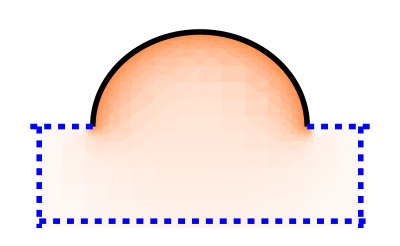

```mathematica
(*Solve diffusion equation in certain geometry (in domain shown below) for D τ = 25.*)
col1=RGBColor[1,135/255,65/255];
Clear[u];
{sol,bd,mesh,rere,gege}=Quiet@SolveDiffusionCirc[2,20,25,2];
p0=Show[DensityPlot[{Evaluate[u[t,x,y]/.sol]/.t->50},Element[{x,y},mesh], PlotRange->{{-bd-0.5,bd+0.5},{-20.5,22},{-0.1,2.5}},PerformanceGoal->"Quality",Mesh->None,AspectRatio->37/60,Frame->None,ColorFunction->(Blend[{White,col1},#1]&),PlotLegends->Placed[BarLegend[{(Blend[{White,col1},#1]&),{0,1}},LabelStyle->{FontFamily->"Arial",Black,FontSize->18},LegendMarkerSize->200,LegendFunction->"Frame",LegendLabel->"c/c_0"],Bottom]],ParametricPlot[{20*{Cos[θ],Sin[θ]},{20+5*θ,0},{-20-5*θ,0},{-bd,-10*θ},{bd,-10*θ},{-bd+20*θ,-20}},{θ,0,π},PlotStyle->{{Thickness[0.01],Black},{Thickness[0.01],Blue,Dashed},{Thickness[0.01],Blue,Dashed},{Thickness[0.01],Blue,Dashed},{Thickness[0.01],Blue,Dashed},{Thickness[0.01],Blue,Dashed}}]]
```

### (e) Concentration curves for different values of √(D τ)κ: numerical vs. analytical results

```mathematica
(*Function to solve diffusion equation for different radii R for both positive and negative curvature. After solving the diffusion equation, the solution is plotted.*)DiffEq[Rad_,Dτval_]:=Module[{p1,x0,y0,Int1,Curv1,Int2,Curv2,sol1,bd1,bd2,sol2,mesh1,mesh2,reg11,reg12,reg21,reg22},{sol1,bd1,mesh1,reg11,reg12}=Quiet@SolveDiffusionCirc[1,Rad,Dτval,1];Clear[{x,y,t,bd,nn}];
{sol2,bd1,mesh2,reg21,reg22}=Quiet@SolveDiffusionCirc[2,Rad,Dτval,1];
(*Plot concentration profile as function of distance at long times t = 50*)
p1=Show[Plot[{Evaluate[u[50,0,yy+Rad]/.sol1]},{yy,0,bd1-Rad},PlotRange->{{-bd1,bd1},{-0.2,2.5}},PlotStyle->Blue],Plot[{Evaluate[u[50,0,-(yy-Rad)]/.sol2]},{yy,0,bd1+Rad},PlotRange->{{-bd1,bd1},{-0.2,2.5}},PlotStyle->Red]];
(*Compute integral of concentration profile along y-axis*)
Int1=Quiet@NIntegrate[Evaluate[u[50,0,yy]/.sol1],{yy,Rad+0.001,bd1}][[1]];
Curv1=1/Rad;
Int2=Quiet@NIntegrate[Evaluate[u[50,0,yy]/.sol2],{yy,-bd1,Rad-0.001}][[1]];
Curv2=-1/Rad;Clear[{yy,u,t,xx,nn}];{p1,Int1,Curv1,Int2,Curv2}]
```

```mathematica
(*Solve for value D τ = 1 for two values of R*)
Dτval2 = 1;
tabsol2=Table[DiffEq[R,Dτval2],{R,{1,5}}];
```

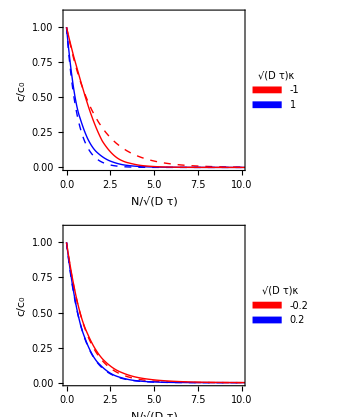

```mathematica
(*Plot numerical solution of concentration together with analytical result.*)p21=Show[Plot[Evaluate@Table[ⅇ^(-(x (κ √(d τ)+√(4+d κ^2 τ)))/(2 √(d τ)))//.{τ->Dτval2,d->1},{κ,{-1,1}}],{x,0,10},PlotRange->{{0,10},{0,1.1}},PlotStyle->{{Red,Dashed},{Blue,Dashed}},FrameLabel->{"N/√(D τ)","c/c_0"},PlotLegends->Placed[SwatchLegend[{Red,Blue},{"-1","1"},LabelStyle->{FontFamily->"Arial",Black,FontSize->18},LegendMarkerSize->12,Alignment->{Center,Center},LegendFunction->"Frame",LegendLabel->"√(D τ)κ"],{0.75,0.5}],AspectRatio->0.5],tabsol2[[1,1]],ImageSize->300];
p22=Show[Plot[Evaluate@Table[ⅇ^(-(x (κ √(d τ)+√(4+d κ^2 τ)))/(2 √(d τ)))//.{τ->Dτval2,d->1},{κ,{-0.2,0.2}}],{x,0,10},PlotRange->{{0,10},{0,1.1}},PlotStyle->{{Red,Dashed},{Blue,Dashed}},FrameLabel->{"N/√(D τ)","c/c_0"},PlotLegends->Placed[SwatchLegend[{Red,Blue},{"-0.2","0.2"},LabelStyle->{FontFamily->"Arial",Black,FontSize->18},LegendMarkerSize->12,Alignment->{Center,Center},LegendFunction->"Frame",LegendLabel->"√(D τ)κ"],{0.75,0.5}],AspectRatio->0.5],tabsol2[[2,1]],ImageSize->300];
p2=GraphicsColumn[{p21,p22},ImageSize->350]
```

### (f) Scan through different values of √(D τ)κ

```mathematica
(*Solve diffusion equation for positive and negative curvature for many values of |κ|.*)
Dτval3 = 1;
tabsol3=Table[DiffEq[1/κ,Dτval3],{κ,{0.025,0.05,0.075,0.1,0.125,0.15,0.15,0.175,0.2,0.3,0.4,0.5,0.6,0.7}}];
```

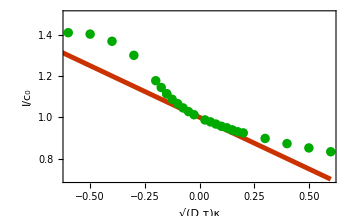

```mathematica
(*Plot resulting solution together with analytical prediction.*)
ConcCurvList={Partition[Riffle[tabsol3[[All,3]],tabsol3[[All,2]]],2],Partition[Riffle[tabsol3[[All,5]],tabsol3[[All,4]]],2]};Dτval=1.;
p3=Show[Plot[Sqrt[Dτval3]-Dτval3/2 κ,{κ,-1,1},PlotRange->{{-0.6,0.6},{0.7,1.5}},PlotStyle->{Thickness[0.01]},FrameLabel->{"√(D τ)κ","I/c_0"},PlotLegends->Placed[{"Analytical"},{0.75,0.7}]],ListPlot[ConcCurvList,PlotStyle->Darker@Green,PlotLegends->Placed[{"Numerical"},{0.75,0.7}]],ImageSize->350]
```